```mathematica
f[p_,ii_, d_]:=If[Mod[ii,2]==0,Cos[p/10000^(2*IntegerPart[ii/2]/d)],Sin[p/10000^(2*IntegerPart[ii/2]/d)]];
Plot[{f[p,1,512],f[p,5,512],f[p,20,512],f[p,15,512]},{p,0,25},PlotLabels->"Expressions"]
```

-Graphics-

```mathematica
f[2,2,512]//N
f[1,1,512]//N
```

-0.350895

0.841471

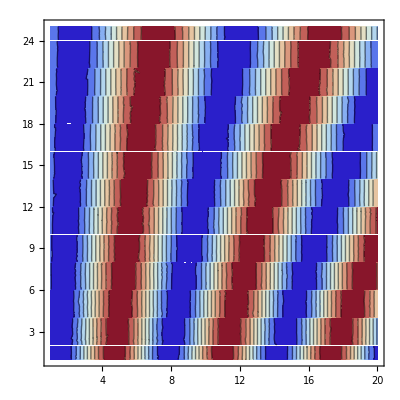

```mathematica
ContourPlot[f[p,ii,512],{p,ii}∈Rectangle[{1,1},{20,25}],ColorFunction->ColorData[{"ThermometerColors","Reverse"}],MaxRecursion->1]
```

```mathematica
Table[f[p,ii,512],{ii,1,5,1},{p,1,5,1}]//N
```

{{0.841471,0.909297,0.14112,-0.756802,-0.958924},{0.569695,-0.350895,-0.969501,-0.753745,0.110692},{0.821856,0.936415,0.245085,-0.657167,-0.993855},{0.597375,-0.286285,-0.939415,-0.836081,-0.0594936},{0.801962,0.958144,0.342782,-0.548606,-0.998229}}